### Start choosing the example:

```mathematica
t=31;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5},Adjacency Matrix→{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{5,U1}},Switching Costs→{}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 80, U1-> 15}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0&&j355-j361-u377+u383==0&&j356-j362-u378+u384==0&&j357-j363-u379+u385==0&&j358-j364-u380+u386==0

EEX: -u377+u382==0.&&-80+u377-u378==0.&&-80+u378-u379==0.&&-80+u379-u380==0.&&-95+u380==0.

D2E: {True,<|j360→80,u387→15,j355→80,j356→80,j357→80,j358→80,j359→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u381→15,u383→-80+335.,u384→-80+255.,u385→-80+175.,u386→-80+95.,u388→335.,u377→335.,u378→255.,u379→175.,u380→95.,u382→335.|>}

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.017087,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→335.,u378→255.,u379→175.,u380→95.,u381→15,u382→335.,u383→-80+335.,u384→-80+255.,u385→-80+175.,u386→-80+95.,u387→15,u388→335.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==77.418&&80.-u378+1. u379==77.418&&80.-u379+1. u380==77.418&&95.-u380==77.418

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==77.418&&80.-u378+1. u379==77.418&&80.-u379+1. u380==77.418&&95.-u380==77.418

FRX1: The Error on the nonlinear terms is 1.77636×10^-15

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→25.3278,u378→22.7459,u379→20.1639,u380→17.582,u381→15,u382→0.+1. 25.3278,u383→0.+1. 22.7459,u384→0.+1. 20.1639,u385→0.+1. 17.582,u386→15.,u387→15,u388→0.+1. 25.3278|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==76.8387&&80.-u378+1. u379==76.8387&&80.-u379+1. u380==76.8387&&95.-u380==76.8387

FRX1: The Error on the nonlinear terms is 7.10543×10^-15

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==76.8387&&80.-u378+1. u379==76.8387&&80.-u379+1. u380==76.8387&&95.-u380==76.8387

FRX1: The Error on the nonlinear terms is 7.10543×10^-15

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→27.6454,u378→24.484,u379→21.3227,u380→18.1613,u381→15,u382→0.+1. 27.6454,u383→0.+1. 24.484,u384→0.+1. 21.3227,u385→0.+1. 18.1613,u386→15.,u387→15,u388→0.+1. 27.6454|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==74.9761&&80.-u378+1. u379==74.9761&&80.-u379+1. u380==74.9761&&95.-u380==74.9761

FRX1: The Error on the nonlinear terms is 1.06581×10^-14

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==74.9761&&80.-u378+1. u379==74.9761&&80.-u379+1. u380==74.9761&&95.-u380==74.9761

FRX1: The Error on the nonlinear terms is 1.06581×10^-14

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→35.0956,u378→30.0717,u379→25.0478,u380→20.0239,u381→15,u382→0.+1. 35.0956,u383→0.+1. 30.0717,u384→0.+1. 25.0478,u385→0.+1. 20.0239,u386→15.,u387→15,u388→0.+1. 35.0956|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==35.034&&80.-u378+1. u379==35.034&&80.-u379+1. u380==35.034&&95.-u380==35.034

FRX1: The Error on the nonlinear terms is 0.

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==35.034&&80.-u378+1. u379==35.034&&80.-u379+1. u380==35.034&&95.-u380==35.034

FRX1: The Error on the nonlinear terms is 0.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→194.864,u378→149.898,u379→104.932,u380→59.966,u381→15,u382→0.+1. 194.864,u383→0.+1. 149.898,u384→0.+1. 104.932,u385→0.+1. 59.966,u386→15.,u387→15,u388→0.+1. 194.864|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==0&&80.-u378+1. u379==0&&80.-u379+1. u380==0&&95.-u380==0

FRX1: The Error on the nonlinear terms is 1.7053×10^-13

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→335.,u378→255.,u379→175.,u380→95.,u381→15,u382→0.+1. 335.,u383→0.+1. 255.,u384→0.+1. 175.,u385→0.+1. 95.,u386→15.,u387→15,u388→0.+1. 335.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-283.906&&80.-u378+1. u379==-283.906&&80.-u379+1. u380==-283.906&&95.-u380==-283.906

FRX1: The Error on the nonlinear terms is 1.13687×10^-13

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-283.906&&80.-u378+1. u379==-283.906&&80.-u379+1. u380==-283.906&&95.-u380==-283.906

FRX1: The Error on the nonlinear terms is 1.13687×10^-13

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→1470.62,u378→1106.72,u379→742.811,u380→378.906,u381→15,u382→0.+1. 1470.62,u383→0.+1. 1106.72,u384→0.+1. 742.811,u385→0.+1. 378.906,u386→15.,u387→15,u388→0.+1. 1470.62|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-22760.5&&80.-u378+1. u379==-22760.5&&80.-u379+1. u380==-22760.5&&95.-u380==-22760.5

FRX1: The Error on the nonlinear terms is 0.

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-22760.5&&80.-u378+1. u379==-22760.5&&80.-u379+1. u380==-22760.5&&95.-u380==-22760.5

FRX1: The Error on the nonlinear terms is 0.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→91376.9,u378→68536.4,u379→45695.9,u380→22855.5,u381→15,u382→0.+1. 91376.9,u383→0.+1. 68536.4,u384→0.+1. 45695.9,u385→0.+1. 22855.5,u386→15.,u387→15,u388→0.+1. 91376.9|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-289963.&&80.-u378+1. u379==-289963.&&80.-u379+1. u380==-289963.&&95.-u380==-289963.

FRX1: The Error on the nonlinear terms is 0.

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-289963.&&80.-u378+1. u379==-289963.&&80.-u379+1. u380==-289963.&&95.-u380==-289963.

FRX1: The Error on the nonlinear terms is 0.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→1.16019×10^6,u378→870144.,u379→580101.,u380→290058.,u381→15,u382→0.+1. 1.16019×10^6,u383→0.+1. 870144.,u384→0.+1. 580101.,u385→0.+1. 290058.,u386→15.,u387→15,u388→0.+1. 1.16019×10^6|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-290863.&&80.-u378+1. u379==-290863.&&80.-u379+1. u380==-290863.&&95.-u380==-290863.

FRX1: The Error on the nonlinear terms is 0.

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-290863.&&80.-u378+1. u379==-290863.&&80.-u379+1. u380==-290863.&&95.-u380==-290863.

FRX1: The Error on the nonlinear terms is 0.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→1.16379×10^6,u378→872843.,u379→581900.,u380→290958.,u381→15,u382→0.+1. 1.16379×10^6,u383→0.+1. 872843.,u384→0.+1. 581900.,u385→0.+1. 290958.,u386→15.,u387→15,u388→0.+1. 1.16379×10^6|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-339107.&&80.-u378+1. u379==-339107.&&80.-u379+1. u380==-339107.&&95.-u380==-339107.

FRX1: The Error on the nonlinear terms is 0.

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-339107.&&80.-u378+1. u379==-339107.&&80.-u379+1. u380==-339107.&&95.-u380==-339107.

FRX1: The Error on the nonlinear terms is 0.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→1.35676×10^6,u378→1.01758×10^6,u379→678389.,u380→339202.,u381→15,u382→0.+1. 1.35676×10^6,u383→0.+1. 1.01758×10^6,u384→0.+1. 678389.,u385→0.+1. 339202.,u386→15.,u387→15,u388→0.+1. 1.35676×10^6|>

```mathematica
alpha = 1.61;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-397981.&&80.-u378+1. u379==-397981.&&80.-u379+1. u380==-397981.&&95.-u380==-397981.

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→335.,u378→255.,u379→175.,u380→95.,u381→15,u382→335.,u383→-80+335.,u384→-80+255.,u385→-80+175.,u386→-80+95.,u387→15,u388→335.|>

```mathematica
alpha = 1.62;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-554286.&&80.-u378+1. u379==-554286.&&80.-u379+1. u380==-554286.&&95.-u380==-554286.

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→335.,u378→255.,u379→175.,u380→95.,u381→15,u382→335.,u383→-80+335.,u384→-80+255.,u385→-80+175.,u386→-80+95.,u387→15,u388→335.|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-1.65381×10^6&&80.-u378+1. u379==-1.65381×10^6&&80.-u379+1. u380==-1.65381×10^6&&95.-u380==-1.65381×10^6

FRX1: The Error on the nonlinear terms is 0.

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-1.65381×10^6&&80.-u378+1. u379==-1.65381×10^6&&80.-u379+1. u380==-1.65381×10^6&&95.-u380==-1.65381×10^6

FRX1: The Error on the nonlinear terms is 0.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→6.61557×10^6,u378→4.96168×10^6,u379→3.30779×10^6,u380→1.6539×10^6,u381→15,u382→0.+1. 6.61557×10^6,u383→0.+1. 4.96168×10^6,u384→0.+1. 3.30779×10^6,u385→0.+1. 1.6539×10^6,u386→15.,u387→15,u388→0.+1. 6.61557×10^6|>

```mathematica
alpha = 1.7;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-1.55949×10^7&&80.-u378+1. u379==-1.55949×10^7&&80.-u379+1. u380==-1.55949×10^7&&95.-u380==-1.55949×10^7

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→335.,u378→255.,u379→175.,u380→95.,u381→15,u382→335.,u383→-80+335.,u384→-80+255.,u385→-80+175.,u386→-80+95.,u387→15,u388→335.|>

```mathematica
alpha = 1.8;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-2.40526×10^10&&80.-u378+1. u379==-2.40526×10^10&&80.-u379+1. u380==-2.40526×10^10&&95.-u380==-2.40526×10^10

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→335.,u378→255.,u379→175.,u380→95.,u381→15,u382→335.,u383→-80+335.,u384→-80+255.,u385→-80+175.,u386→-80+95.,u387→15,u388→335.|>

```mathematica
alpha = 1.89;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-2.08807×10^17&&80.-u378+1. u379==-2.08807×10^17&&80.-u379+1. u380==-2.08807×10^17&&95.-u380==-2.08807×10^17

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→335.,u378→255.,u379→175.,u380→95.,u381→15,u382→335.,u383→-80+335.,u384→-80+255.,u385→-80+175.,u386→-80+95.,u387→15,u388→335.|>

```mathematica
alpha = 1.9;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-5.6037×10^18&&80.-u378+1. u379==-5.6037×10^18&&80.-u379+1. u380==-5.6037×10^18&&95.-u380==-5.6037×10^18

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→335.,u378→255.,u379→175.,u380→95.,u381→15,u382→335.,u383→-80+335.,u384→-80+255.,u385→-80+175.,u386→-80+95.,u387→15,u388→335.|>

```mathematica
alpha = 1.95;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-7.54344×10^32&&80.-u378+1. u379==-7.54344×10^32&&80.-u379+1. u380==-7.54344×10^32&&95.-u380==-7.54344×10^32

FRX1: The Error on the nonlinear terms is 0.

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-7.54344×10^32&&80.-u378+1. u379==-7.54344×10^32&&80.-u379+1. u380==-7.54344×10^32&&95.-u380==-7.54344×10^32

FRX1: The Error on the nonlinear terms is 0.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→3.01738×10^33,u378→2.26303×10^33,u379→1.50869×10^33,u380→7.54344×10^32,u381→15,u382→0.+1. 3.01738×10^33,u383→0.+1. 2.26303×10^33,u384→0.+1. 1.50869×10^33,u385→0.+1. 7.54344×10^32,u386→15.,u387→15,u388→0.+1. 3.01738×10^33|>

```mathematica
alpha = 1.99;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-1.99061×10^105&&80.-u378+1. u379==-1.99061×10^105&&80.-u379+1. u380==-1.99061×10^105&&95.-u380==-1.99061×10^105

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→335.,u378→255.,u379→175.,u380→95.,u381→15,u382→335.,u383→-80+335.,u384→-80+255.,u385→-80+175.,u386→-80+95.,u387→15,u388→335.|>

```mathematica
alpha = 1.999;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-1.7336×10^106&&80.-u378+1. u379==-1.7336×10^106&&80.-u379+1. u380==-1.7336×10^106&&95.-u380==-1.7336×10^106

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→335.,u378→255.,u379→175.,u380→95.,u381→15,u382→335.,u383→-80+335.,u384→-80+255.,u385→-80+175.,u386→-80+95.,u387→15,u388→335.|>

```mathematica
alpha = 2;
FFR=Catch @FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

EEX: j361==jt367&&j360==jt368&&j355==jt369&&j362==jt370&&j356==jt371&&j363==jt372&&j357==jt373&&j364==jt374&&j358==jt375&&j365==jt376&&j355==jt368&&j366==jt367&&j361==jt370&&j356==jt369&&j362==jt372&&j357==jt371&&j363==jt374&&j358==jt373&&j364==jt376&&j359==jt375&&j360==80&&u387==15&&-u382+u388==0&&-u381+u387==0&&jt367==0&&jt376==0

EEX: -u377+u382==0.&&-u378+u383==0.&&-u379+u384==0.&&-u380+u385==0.&&-15+u386==0.

EEX: 80.-u377+1. u378==-2.2049×10^106&&80.-u378+1. u379==-2.2049×10^106&&80.-u379+1. u380==-2.2049×10^106&&95.-u380==-2.2049×10^106

The last system in the iteration was inconsistent.
Throwing the last feasible solution.

<|j355→80,j356→80,j357→80,j358→80,j359→80,j360→80,j361→0,j362→0,j363→0,j364→0,j365→0,j366→0,jt367→0,jt368→80,jt369→80,jt370→0,jt371→80,jt372→0,jt373→80,jt374→0,jt375→80,jt376→0,u377→335.,u378→255.,u379→175.,u380→95.,u381→15,u382→335.,u383→-80+335.,u384→-80+255.,u385→-80+175.,u386→-80+95.,u387→15,u388→335.|>

### What we this plot for?

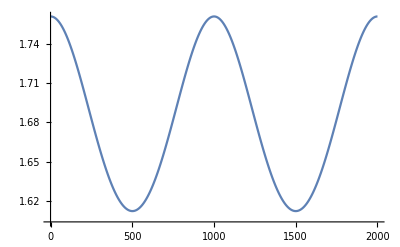

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.